```mathematica
dirStr = NotebookDirectory[]~StringJoin~"Utils.nb";

NotebookEvaluate[dirStr];
NotebookEvaluate[dirStr];
```

```mathematica
(*We specify the Hamiltonian in pieces*)
term1 = p[1]^2/(2m) - 1/2 m λ^2 q[1]^2;
term2 = 0;
term3 = G4[1] q[1]^4;

eigs = {-I λ};
prs = {{p[1], q[1]}};

(*Some symplectic transformations used below. x' = (x - I p)/√2 = Sqrt[ℏ] a^† (the raising operator).
Similarly, p' = (p - I x)/√2 = -I Sqrt[ℏ] a (lowering operator).*)
scaleRule = {q[1] -> q[1]/Sqrt[m λ],
			p[1] -> Sqrt[m λ]p[1]};
diagRule = {q[1] -> I/Sqrt[2](q[1] + p[1]),
			p[1] -> -I/Sqrt[2](p[1] - q[1])};

(*Choose degeneracy:*)
(*Ω = ω;*)

(*We rescale and diagonalize the Hamiltonian, what we obtain we assign to H[n, m].
Here, n is the order of the term and m is the order of the QNF, which starts at 2.*)
H[0, 2] = 0;
H[1, 2] = 0;
H[2, 2] = Expand[term1 /. scaleRule /. diagRule];
H[3, 2] = Expand[term2 /. scaleRule /. diagRule];
H[4, 2] = Expand[term3 /. scaleRule /. diagRule];
H[n_ ? (# > 4 &), 2] := 0;

H[2, 2]
H[3, 2]
H[4, 2]

QNFOrd = 12;
QNFSymb = computeQNFSymbUpToOrder[QNFOrd]

(*success = Table[MB[QNFSymb[[3]], QNFSymb[[k]]], {k, 1, Length[QNFSymb]}] == ConstantArray[0, QNFOrd + 1]

If[success,
	Print["Normalization was successful, saving to file..."];
	saveDir = NotebookDirectory[]~StringJoin~"QNF.wl";
	Save[saveDir, {prs, QNFSymb}]
]*)

Table[{k - 1, MB[QNFSymb[[3]], QNFSymb[[k]]]}, {k, 5, Length[QNFSymb], 2}]
```

λ p[1] q[1]

0

(G4[1] p[1]^4)/(4 m^2 λ^2)+(G4[1] p[1]^3 q[1])/(m^2 λ^2)+(3 G4[1] p[1]^2 q[1]^2)/(2 m^2 λ^2)+(G4[1] p[1] q[1]^3)/(m^2 λ^2)+(G4[1] q[1]^4)/(4 m^2 λ^2)

{0,0,λ p[1] q[1],0,(3 G4[1] p[1]^2 q[1]^2)/(2 m^2 λ^2),0,-(9 ℏ^2 G4[1]^2 p[1] q[1])/(8 m^4 λ^5)-(17 G4[1]^2 p[1]^3 q[1]^3)/(4 m^4 λ^5),0,(459 ℏ^2 G4[1]^3 p[1]^2 q[1]^2)/(16 m^6 λ^8)+(375 G4[1]^3 p[1]^4 q[1]^4)/(16 m^6 λ^8),0,-(4095 ℏ^4 G4[1]^4 p[1] q[1])/(64 m^8 λ^11)-(35585 ℏ^2 G4[1]^4 p[1]^3 q[1]^3)/(64 m^8 λ^11)-(10689 G4[1]^4 p[1]^5 q[1]^5)/(64 m^8 λ^11),0,(1352457 ℏ^4 G4[1]^5 p[1]^2 q[1]^2)/(256 m^10 λ^14)+(2466135 ℏ^2 G4[1]^5 p[1]^4 q[1]^4)/(256 m^10 λ^14)+(87549 G4[1]^5 p[1]^6 q[1]^6)/(64 m^10 λ^14)}

{{4,0},{6,0},{8,0},{10,0},{12,0}}

```mathematica
(*saveDir = NotebookDirectory[]~StringJoin~"QNF.wl";
Get[saveDir]*)
```

```mathematica
(*ClearAll[quant];
quant[m_, n_, {P_, Q_}] := Sum[1/2^n Binomial[n, k1] NonCommutativeMultiply @@ (Table[Q, {k2, 1, k1}]~Join~Table[P, {k2, 1, m}]~Join~Table[Q, {k2, 1, n-k1}]), {k1, 0, n}];
quant[1, 0, {P_, Q_}] := P;
quant[0, 1, {P_, Q_}] := Q;
quant[0, 0, {P_, Q_}] := 1;

ClearAll[coeffToQuant];
coeffToQuant[powVec_] := Module[{prods = {}, length},
	Do[
		prods = Append[prods, quant[powVec[[2k - 1]], powVec[[2k]], prs[[k]]]],
		{k, 1, Length[prs]}
	];
	
	prods = DeleteElements[prods, {1}];
	
	length = Length[prods];
	Return[
		Which[
			length > 1, NonCommutativeMultiply @@ prods,
			length == 1, First @ prods,
			length == 0, 1
		]
	]
];

ClearAll[WignerWeylQuant];
WignerWeylQuant[expr_] := Module[
	{coeffRules = CoefficientRules[expr, Flatten[prs]], coeffs, monoms, quantMonoms, res},
	coeffs = Part[#, 2] & /@ coeffRules;
	monoms = Part[#, 1] & /@ coeffRules;
	quantMonoms = coeffToQuant /@ monoms;
	res = Sum[coeffs[[k]]quantMonoms[[k]], {k, 1, Length[coeffs]}];
	Return[res]
];

QNF = WignerWeylQuant /@ QNFSymb

Needs["NC`"];
Needs["NCAlgebra`"];

SetCommutative[{m, ℏ, g3, λ3, g4, λ4, ω}];
SetNonCommutative[{p, q}];

QNF = NCExpand[QNF]*)
```

```mathematica
(*(*Takes into account that p = -I Sqrt[ℏ] a and q = Sqrt[ℏ] a^†, hence because [a, a^†] = 1: p ** q = q ** p - I ℏ.*)
SetNonCommutative[left, right];
ClearAll[nrmOrdRule];
nrmOrdRule = Table[
	NonCommutativeMultiply[left___, prs[[k, 1]], prs[[k, 2]], right___] ->
	NonCommutativeMultiply[left, prs[[k, 2]], prs[[k, 1]], right] +
	(-I ℏ) NonCommutativeMultiply[left, right],
	{k, 1, Length[prs]}
];

ClearAll[needsReordering];
needsReordering[op1_, op2_] := Position[prs, op1][[1, 1]] > Position[prs, op2][[1, 1]];

ClearAll[commuteRule];
commuteRule = {
	NonCommutativeMultiply[left___, s1_, s2_, right___] /; needsReordering[s1, s2] :>
	NonCommutativeMultiply[left, s2, s1, right]
};

ClearAll[joinedRule];
joinedRule = commuteRule~Join~nrmOrdRule;

QNFNormalOrdered = NCExpand[QNF //. joinedRule]*)
```

```mathematica
(*(*Verifies whether the Hamiltonian is still in NF.*)
commuteNO[expr1_, expr2_] := NCExpand[NCExpand[expr1 ** expr2] //. joinedRule] - NCExpand[NCExpand[expr2 ** expr1] //. joinedRule];

Table[{k - 1, commuteNO[QNFNormalOrdered[[3]], QNFNormalOrdered[[k]]]}, {k, 5, Length[QNFNormalOrdered], 2}]*)
```

```mathematica
With[{rule = symbRule[45], ruleInv = symbRuleInv[45]},
	ClearAll[JRule];
	JRule = {prs[[1, 1]] prs[[1, 2]] -> J[1], prs[[1, 1]]^n_ prs[[1, 2]]^n_ -> J[1]^n}~Join~Flatten[Table[{prs[[k, 1]] prs[[k, 2]] -> -I J[k], prs[[k, 1]]^n_ prs[[k, 2]]^n_ -> (-I)^n J[k]^n}, {k, 2, Length[prs]}]] /. rule;
	QNFSymbActions = QNFSymb /. rule //. JRule
]

ClearAll[Op];
Op[J[1], n_] := Expand[OverHat[J[1]]Op[J[1], n-1] - (ℏ/2)^2 (n-1)^2 Op[J[1], n-2]];
Op[J[1], 1] := OverHat[J[1]];
Op[J[1], 0] := 1;
Op[J[m_ /; m>=2], n_] := Expand[OverHat[J[m]]Op[J[m], n-1] + (ℏ/2)^2 (n-1)^2 Op[J[m], n-2]];
Op[J[m_ /; m>=2], 1] := OverHat[J[m]];
Op[J[m_ /; m>=2], 0] := 1;

ClearAll[opRule];
opRule = {J[m_] :> Op[J[m], 1], J[m_]^n_ :> Op[J[m], n]};

QNFActions = QNFSymbActions /. opRule
QNFActions = Expand[QNFActions]

ClearAll[nRule];
nRule = {OverHat[J[m_ /; m>=2]] -> ℏ(n[m] + 1/2)};

QNFExplicitQuantumNumbers = Total[Expand[QNFActions /. nRule]]
```

{0,0,λ J[1],0,(3 G4[1] J[1]^2)/(2 m^2 λ^2),0,-(9 ℏ^2 G4[1]^2 J[1])/(8 m^4 λ^5)-(17 G4[1]^2 J[1]^3)/(4 m^4 λ^5),0,(459 ℏ^2 G4[1]^3 J[1]^2)/(16 m^6 λ^8)+(375 G4[1]^3 J[1]^4)/(16 m^6 λ^8),0,-(4095 ℏ^4 G4[1]^4 J[1])/(64 m^8 λ^11)-(35585 ℏ^2 G4[1]^4 J[1]^3)/(64 m^8 λ^11)-(10689 G4[1]^4 J[1]^5)/(64 m^8 λ^11),0,(1352457 ℏ^4 G4[1]^5 J[1]^2)/(256 m^10 λ^14)+(2466135 ℏ^2 G4[1]^5 J[1]^4)/(256 m^10 λ^14)+(87549 G4[1]^5 J[1]^6)/(64 m^10 λ^14)}

{0,0,λ OverHat[J[1]],0,(3 G4[1] (-ℏ^2/4+OverHat[J[1]]^2))/(2 m^2 λ^2),0,-(9 ℏ^2 G4[1]^2 OverHat[J[1]])/(8 m^4 λ^5)-(17 G4[1]^2 (-5/4 ℏ^2 OverHat[J[1]]+OverHat[J[1]]^3))/(4 m^4 λ^5),0,(459 ℏ^2 G4[1]^3 (-ℏ^2/4+OverHat[J[1]]^2))/(16 m^6 λ^8)+(375 G4[1]^3 ((9 ℏ^4)/16-7/2 ℏ^2 OverHat[J[1]]^2+OverHat[J[1]]^4))/(16 m^6 λ^8),0,-(4095 ℏ^4 G4[1]^4 OverHat[J[1]])/(64 m^8 λ^11)-(35585 ℏ^2 G4[1]^4 (-5/4 ℏ^2 OverHat[J[1]]+OverHat[J[1]]^3))/(64 m^8 λ^11)-(10689 G4[1]^4 (89/16 ℏ^4 OverHat[J[1]]-15/2 ℏ^2 OverHat[J[1]]^3+OverHat[J[1]]^5))/(64 m^8 λ^11),0,(1352457 ℏ^4 G4[1]^5 (-ℏ^2/4+OverHat[J[1]]^2))/(256 m^10 λ^14)+(2466135 ℏ^2 G4[1]^5 ((9 ℏ^4)/16-7/2 ℏ^2 OverHat[J[1]]^2+OverHat[J[1]]^4))/(256 m^10 λ^14)+(87549 G4[1]^5 (-(225 ℏ^6)/64+439/16 ℏ^4 OverHat[J[1]]^2-55/4 ℏ^2 OverHat[J[1]]^4+OverHat[J[1]]^6))/(64 m^10 λ^14)}

{0,0,λ OverHat[J[1]],0,-(3 ℏ^2 G4[1])/(8 m^2 λ^2)+(3 G4[1] OverHat[J[1]]^2)/(2 m^2 λ^2),0,(67 ℏ^2 G4[1]^2 OverHat[J[1]])/(16 m^4 λ^5)-(17 G4[1]^2 OverHat[J[1]]^3)/(4 m^4 λ^5),0,(1539 ℏ^4 G4[1]^3)/(256 m^6 λ^8)-(1707 ℏ^2 G4[1]^3 OverHat[J[1]]^2)/(32 m^6 λ^8)+(375 G4[1]^3 OverHat[J[1]]^4)/(16 m^6 λ^8),0,-(305141 ℏ^4 G4[1]^4 OverHat[J[1]])/(1024 m^8 λ^11)+(89165 ℏ^2 G4[1]^4 OverHat[J[1]]^3)/(128 m^8 λ^11)-(10689 G4[1]^4 OverHat[J[1]]^5)/(64 m^8 λ^11),0,-(1456569 ℏ^6 G4[1]^5)/(2048 m^10 λ^14)+(9317949 ℏ^4 G4[1]^5 OverHat[J[1]]^2)/(1024 m^10 λ^14)-(587265 ℏ^2 G4[1]^5 OverHat[J[1]]^4)/(64 m^10 λ^14)+(87549 G4[1]^5 OverHat[J[1]]^6)/(64 m^10 λ^14)}

-(3 ℏ^2 G4[1])/(8 m^2 λ^2)+(1539 ℏ^4 G4[1]^3)/(256 m^6 λ^8)-(1456569 ℏ^6 G4[1]^5)/(2048 m^10 λ^14)+λ OverHat[J[1]]+(67 ℏ^2 G4[1]^2 OverHat[J[1]])/(16 m^4 λ^5)-(305141 ℏ^4 G4[1]^4 OverHat[J[1]])/(1024 m^8 λ^11)+(3 G4[1] OverHat[J[1]]^2)/(2 m^2 λ^2)-(1707 ℏ^2 G4[1]^3 OverHat[J[1]]^2)/(32 m^6 λ^8)+(9317949 ℏ^4 G4[1]^5 OverHat[J[1]]^2)/(1024 m^10 λ^14)-(17 G4[1]^2 OverHat[J[1]]^3)/(4 m^4 λ^5)+(89165 ℏ^2 G4[1]^4 OverHat[J[1]]^3)/(128 m^8 λ^11)+(375 G4[1]^3 OverHat[J[1]]^4)/(16 m^6 λ^8)-(587265 ℏ^2 G4[1]^5 OverHat[J[1]]^4)/(64 m^10 λ^14)-(10689 G4[1]^4 OverHat[J[1]]^5)/(64 m^8 λ^11)+(87549 G4[1]^5 OverHat[J[1]]^6)/(64 m^10 λ^14)

```mathematica
ClearAll[unitRule, Ε, maxPowerG, specialSeries, specialSeriesJCoeffs, ΝClassical, diffOp, ΝSeries, ΝSeriesTerm, ΝDirect]

unitRule = {β -> kg^-1 m^-2 s^2, m -> kg, ℏ -> kg m^2 s^-1, λ -> s^-1, G4[n_] -> kg m^-2 s^-2};

Ε[J_] = QNFExplicitQuantumNumbers /. {OverHat[J[1]] -> J};

maxPowerG = Length[CoefficientList[Ε[J], G4[1]]] - 1;

(*specialSeries = Collect[Normal[Series[Exp[-β(Ε[J] - λ J)] D[Ε[J], J] / λ, {G4[1], 0, maxPowerG}]], G4[1], Expand];*)
(*specialSeries = Collect[Normal[Series[Expand[# - D[#, J]/(β λ)] & @ Exp[-β(Ε[J] - λ J)], {G4[1], 0, maxPowerG}]], G4[1], Expand];*)

specialSeries = Collect[Normal[Series[Exp[-β(Ε[J] - λ J)], {G4[1], 0, maxPowerG}]], G4[1], Expand]; (*(incorrect) specialSeries*)
specialSeriesJCoeffs = CoefficientList[specialSeries, J];

(*Missing the *)
ΝClassical[β_] = λ / (4 π) Csc[β ℏ λ / 2] Exp[-β Esph];
(*== λ / (2 π ℏ) Integrate[Exp[-β (Esph + λ J)] / (1 + Exp[-2 π J / ℏ]), {J, -Infinity, Infinity}, Assumptions -> {β > 0, ℏ > 0, λ > 0}]*)

diffOp = specialSeriesJCoeffs.Table[Expand[Nest[Expand[- (Esph # + D[#, β]) / λ] &, #, k]], {k, 0, Length[specialSeriesJCoeffs] - 1}] &;

ΝSeries[β_] = Collect[Expand[diffOp[ΝClassical[β]]/ΝClassical[β]], G4[1]];
ΝSeries[β_, 0] = 1;
ΝSeries[β_, n_ /; 1 <= n <= maxPowerG] := ΝSeries[β, n] = ΝSeries[β] /. {G4[1]^m_ /; m > n -> 0}

ΝSeriesTerm[β_, 0] = 1;
ΝSeriesTerm[β_, n_ /; 1 <= n <= maxPowerG] := ΝSeries[β, n] - ΝSeries[β, n - 1]

ΝDirect[β_, n_ /; 0 <= n <= maxPowerG] := ΝClassical[β] ΝSeries[β, n]
```

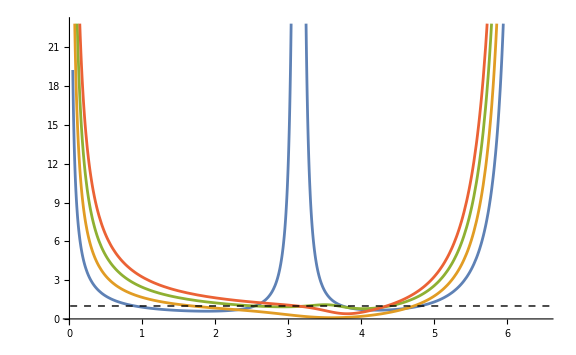

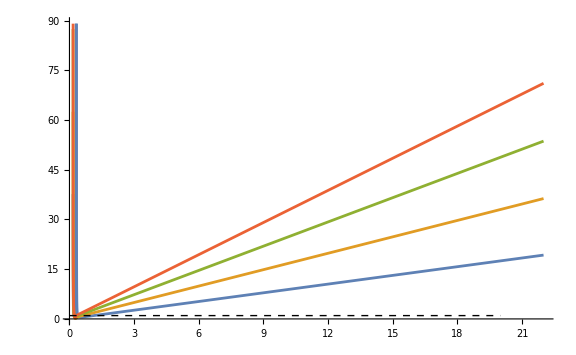

```mathematica
replConsts = {ℏ -> 1, m -> 1, λ -> 1, G4[1] -> 0.05, Esph -> 80.0};
βMin = 1/22.0;
βMax = 6.5;

pltΝSeriesRatiosβ = Plot[
	Evaluate[Table[Abs[ΝSeriesTerm[β, k + 1] / ΝSeriesTerm[β, k]], {k, 1, maxPowerG - 1}] /. replConsts],
	{β, βMin, βMax},
	ImageSize -> Large,
	Epilog -> {Directive[{Black, Dashed}], Line[{{0.01, 1}, {20.0, 1}}]}
]

pltΝSeriesRatiosTemp = Plot[
	Evaluate[Table[Abs[ΝSeriesTerm[1/kT, k + 1] / ΝSeriesTerm[1/kT, k]], {k, 1, maxPowerG - 1}] /. replConsts],
	{kT, 1/βMax, 1/βMin},
	ImageSize -> Large,
	Epilog -> {Directive[{Black, Dashed}], Line[{{0.01, 1}, {20.0, 1}}]}
]
```

```mathematica
ClearAll[ΦSeries, ΦSeriesTerm, Ν]

ΦSeries[β_] = Expand[Normal[Series[-Log[ΝSeries[β]] / β, {G4[1], 0, maxPowerG}]]];
ΦSeries[β_, 0] = 0;
ΦSeries[β_, n_ /; 1 <= n <= maxPowerG] := ΦSeries[β, n] = ΦSeries[β] /. {G4[1]^m_ /; m > n -> 0}

ΦSeriesTerm[β_, 0] = 0;
ΦSeriesTerm[β_, n_ /; 1 <= n <= maxPowerG] := ΦSeries[β, n] - ΦSeries[β, n - 1]

Ν[β_, n_ /; 0 <= n <= maxPowerG] := Ν[β, n] = ΝClassical[β] Exp[-β ΦSeries[β, n]]

saveDir = NotebookDirectory[]~StringJoin~"RateNumeratorSave.wl";
Save[saveDir, {ΝSeries, ΝSeriesTerm, ΝDirect, ΦSeries, ΦSeriesTerm, Ν}]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387]}

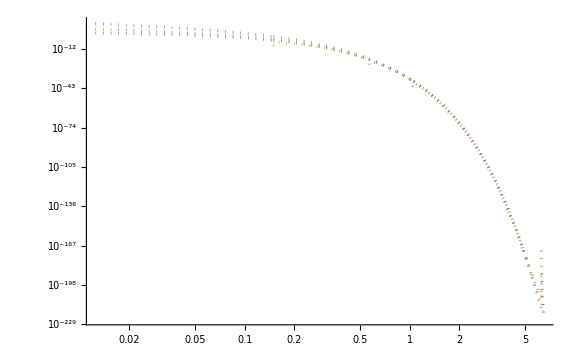

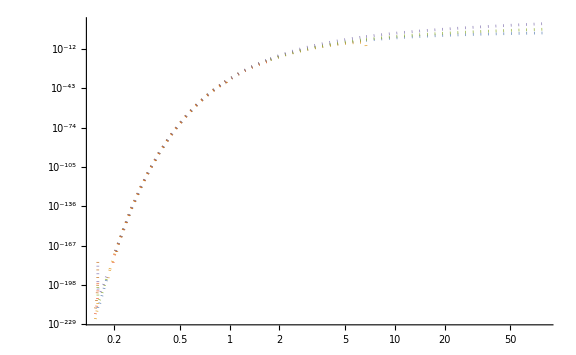

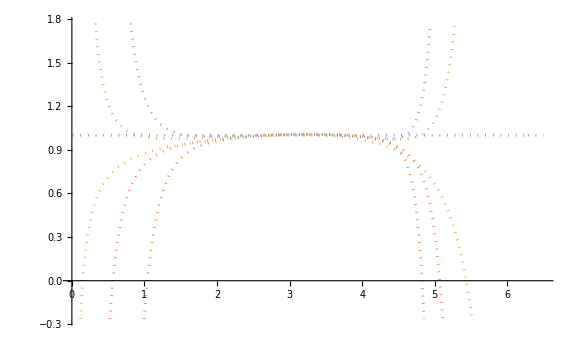

```mathematica
ϵ = 0.05;
replConsts = {ℏ -> 1, m -> 1, λ -> 1, G4[1] -> ϵ, Esph -> 80.0};
βMin = 1/80.0;
βMax = 6.5;

ColorData[97, "ColorList"][[1 ;; maxPowerG + 1]]

logLogPltΝDirectβ = LogLogPlot[
	Evaluate[Table[ΝDirect[β, k] /. replConsts, {k, 0, maxPowerG}]],
	{β, βMin, βMax},
	ImageSize -> Large,
	PlotStyle -> Dotted
]

logLogPltΝDirectTemp = LogLogPlot[
	Evaluate[Table[ΝDirect[1/kT, k] /. replConsts, {k, 0, maxPowerG}]],
	{kT, 1/βMax, 1/βMin},
	ImageSize -> Large,
	PlotStyle -> Dotted
]

pltΝSeriesβ = Plot[
	Evaluate[Table[ΝSeries[β, k] /. replConsts, {k, 0, maxPowerG}]],
	{β, βMin, βMax},
	ImageSize -> Large,
	PlotStyle -> Dotted
]
```

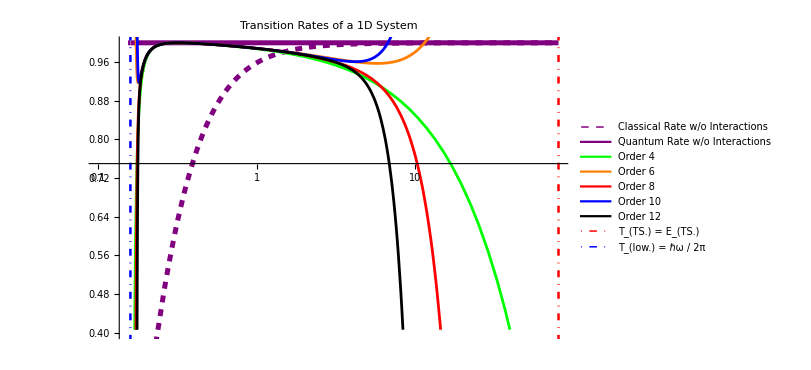

C:\Users\User\OneDrive\Desktop\MSc Thesis\Gianni's work\PhD Final Archive\PhD Final Archive\Mathematica Programs\QNF Code (NEW Comparing Z via PI with Z via QNFs)\1D_0.005_QNF_12.png

```mathematica
ϵ = 0.005;
replConsts = {ℏ -> 1, m -> 1, λ -> 1, G4[1] -> ϵ, Esph -> 80.0};
βMin = 1/80.0;
βMax = 6.5;

NSeriesData = Table[ΝSeries[1/kT, k] /. replConsts, {k, 0, maxPowerG}];
Ord0 = NSeriesData[[1]];
Ord4 = NSeriesData[[2]];
Ord6 = NSeriesData[[3]];
Ord8 = NSeriesData[[4]];
Ord10 = NSeriesData[[5]];
Ord12 = NSeriesData[[6]];

ΓClassical[β_] = ((1/(2π ℏ β))*Exp[-β Esph])/ΝClassical[β] /. replConsts;
(*ΝClassical[β_] = λ / (4 π) Csc[β ℏ λ / 2] Exp[-β Esph]*)

pltΝSeriesTemp = Legended[
	Show[
	LogLinearPlot[Evaluate[ΓClassical[1/kT]],
		{kT, 1/10, 1/βMin},
		PlotStyle -> {Purple, Dashed, Thickness[0.006]}],
	LogLinearPlot[
	{Ord0, Ord4, Ord6, Ord8,Ord10,Ord12},{kT, 1/βMax, 1/βMin},
	PlotStyle -> {{Purple, Thickness[0.006]}, Green, Orange, Red, Blue, Black}],
	AxesLabel -> {"T"},
	AxesOrigin -> {-2,0.75},
	ImageSize -> 600,
	PlotRange -> {0.4,1},
	PlotLabel -> "Transition Rates of a 1D System",
	LabelStyle -> {FontSize -> 16},
			Epilog -> {
					{Red, DotDashed, Thickness[0.003], Line[{{Log[80], 0}, {Log[80], 2}}]},
					{Blue, DotDashed, Thickness[0.003], Line[{{Log[1/(2π)], 0}, {Log[1/(2π)], 2}}]}(*,
					{Orange, DotDashed, Thickness[0.003], Line[{{Log[1], 0}, {Log[1], 2}}]}*)
				}
	],
{
Placed[LineLegend[{Directive[Purple, Dashed, Thickness[2 0.003]]}, {"Classical Rate w/o Interactions"}, LabelStyle -> {FontSize -> 16}], Right],
Placed[LineLegend[{Purple, Green, Orange, Red, Blue, Black}, {"Quantum Rate w/o Interactions","Order 4","Order 6","Order 8","Order 10","Order 12"}, LabelStyle -> {FontSize -> 16}], Right],
Placed[LineLegend[{Directive[Red, DotDashed, Thickness[2 0.003]]}, {"T_(TS.) = E_(TS.)"}, LabelStyle -> {FontSize -> 16}], Right],
(*Placed[LineLegend[{Directive[Orange, DotDashed, Thickness[2 0.003]]}, {"T_(grd.) = ℏω"}, LabelStyle -> {FontSize -> 16}], Right],*)
Placed[LineLegend[{Directive[Blue, DotDashed, Thickness[2 0.003]]}, {"T_(low.) = ℏω / 2π"}, LabelStyle -> {FontSize -> 16}], Right]}
]

imgDir = NotebookDirectory[]~StringJoin~"1D_"~StringJoin~ToString[ϵ]~StringJoin~"_QNF_"~StringJoin~ToString[QNFOrd]~StringJoin~".png";
Export[imgDir, pltΝSeriesTemp]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387]}

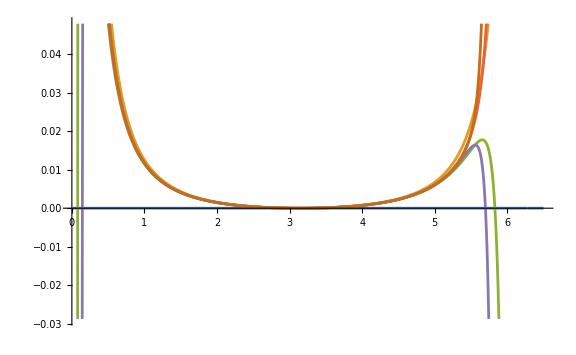

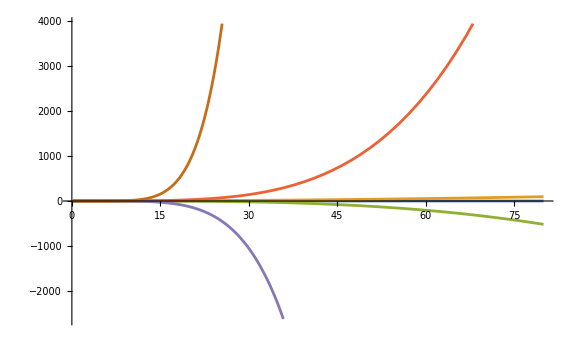

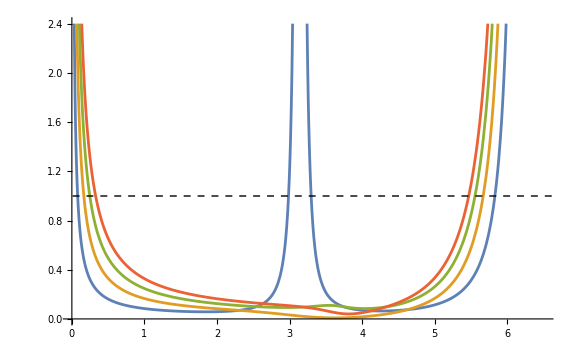

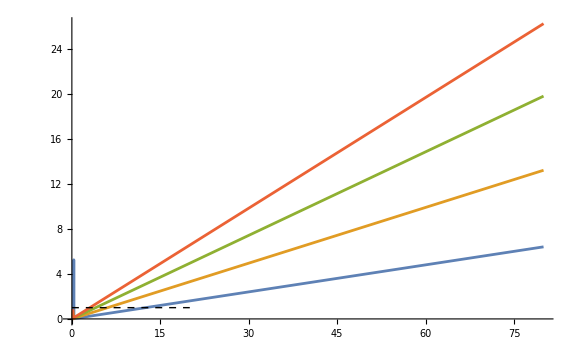

General::munfl: Exp[-50631.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-26617.6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-13984.9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

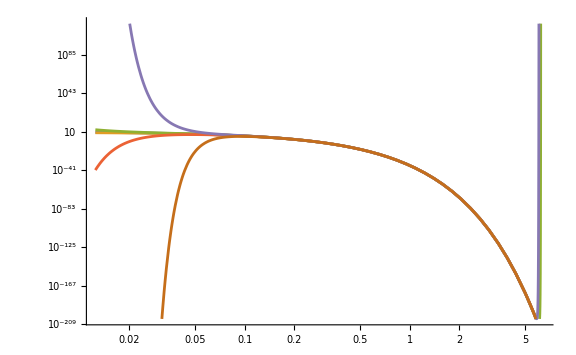

General::munfl: Exp[-35745.4] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

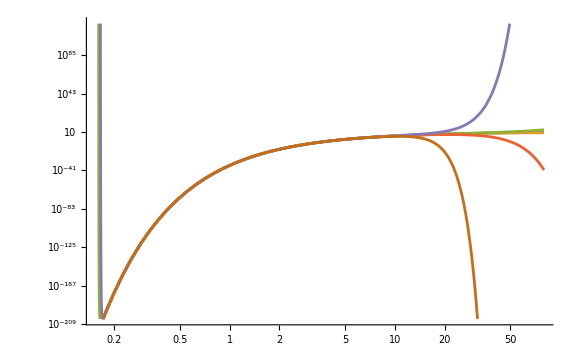

```mathematica
ColorData[97, "ColorList"][[1 ;; maxPowerG + 1]]
pltΦSeriesβ = Plot[
	Evaluate[Table[ΦSeries[β, k] /. replConsts, {k, 0, maxPowerG}]],
	{β, βMin, βMax},
	ImageSize -> Large
]

pltΦSeriesTemp = Plot[
	Evaluate[Table[ΦSeries[1/kT, k] /. replConsts, {k, 0, maxPowerG}]],
	{kT, 1/βMax, 1/βMin},
	ImageSize -> Large
]

pltΦSeriesRatiosβ = Plot[
	Evaluate[Table[Abs[ΦSeriesTerm[β, k + 1] / ΦSeriesTerm[β, k]], {k, 1, maxPowerG - 1}] /. replConsts],
	{β, βMin, βMax},
	ImageSize -> Large,
	Epilog -> {Directive[{Black, Dashed}], Line[{{0.01, 1}, {20.0, 1}}]}
]

pltΦSeriesRatiosTemp = Plot[
	Evaluate[Table[Abs[ΦSeriesTerm[1/kT, k + 1] / ΦSeriesTerm[1/kT, k]], {k, 1, maxPowerG - 1}] /. replConsts],
	{kT, 1/βMax, 1/βMin},
	ImageSize -> Large,
	Epilog -> {Directive[{Black, Dashed}], Line[{{0.01, 1}, {20.0, 1}}]}
]

logLogPltΝβ = LogLogPlot[
	Evaluate[Table[Ν[β, k] /. replConsts, {k, 0, maxPowerG}]],
	{β, βMin, βMax},
	ImageSize -> Large
]

logLogPltΝTemp = LogLogPlot[
	Evaluate[Table[Ν[1/kT, k] /. replConsts, {k, 0, maxPowerG}]],
	{kT, 1/βMax, 1/βMin},
	ImageSize -> Large
]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387]}

General::munfl: Exp[-48042.4] is too small to represent as a normalized machine number; precision may be lost.

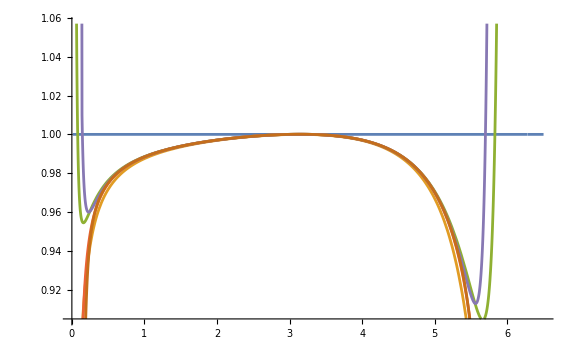

General::munfl: Exp[-1032.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.38535×10^6] is too small to represent as a normalized machine number; precision may be lost.

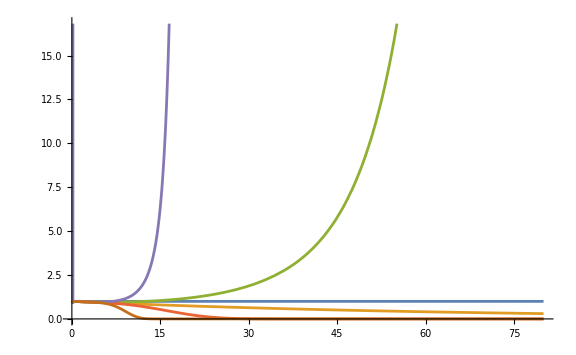

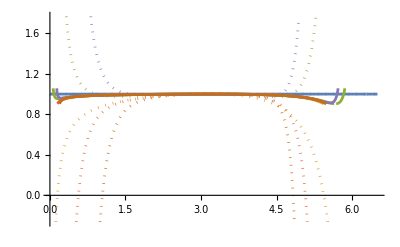

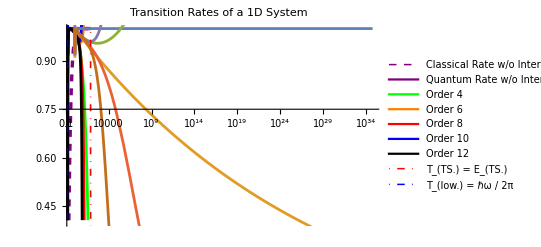

```mathematica
ColorData[97, "ColorList"][[1 ;; maxPowerG + 1]]
pltΝSeriesResummedβ = Plot[
	Evaluate[Table[Exp[-β ΦSeries[β, k]] /. replConsts, {k, 0, maxPowerG}]],
	{β, βMin, βMax},
	ImageSize -> Large
]

pltΝSeriesResummedTemp = Plot[
	Evaluate[Table[Exp[-ΦSeries[1/kT, k] / kT] /. replConsts, {k, 0, maxPowerG}]],
	{kT, 1/βMax, 1/βMin},
	ImageSize -> Large
]

Show[{pltΝSeriesβ, pltΝSeriesResummedβ}, ImageSize -> Full]
Show[{pltΝSeriesTemp, pltΝSeriesResummedTemp}, ImageSize -> Full]
```